```mathematica
lista = {a,b,c}
```

{a,b,c}

```mathematica
lista[[0]]
```

List

```mathematica
lista /. {List -> Times } /. Times-> Plus
```

a+b+c

```mathematica
FullForm[ a+b+c ]
```

Plus[a,b,c]

```mathematica
l1 = Table[ a[i], {i,1,4}]
```

{a[1],a[2],a[3],a[4]}

```mathematica
l2 = Table[ b[i], {i,1,4}]
```

{b[1],b[2],b[3],b[4]}

```mathematica
l1.l2
```

a[1] b[1]+a[2] b[2]+a[3] b[3]+a[4] b[4]

```mathematica
M = Table[ c[i,j], {i,1,2},{j,1,4}]
```

{{c[1,1],c[1,2],c[1,3],c[1,4]},{c[2,1],c[2,2],c[2,3],c[2,4]}}

```mathematica
l3 = Table[ tmp=i^2; tmp2 = Sin[tmp]; tmp2, {i,1,4}]
```

{Sin[1],Sin[4],Sin[9],Sin[16]}

```mathematica
NDSolve[ {y''[t] + 9 y[t] == 0, y[0]==0, y'[0]==1}, y[t], {t,0,10}]
```

{{y[t]→InterpolatingFunction[…][t]}}

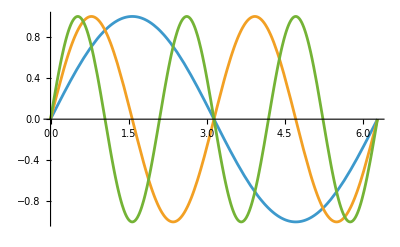

```mathematica
Plot[ {Sin[x], Sin[2 x], Sin[3 x]}, {x,0,2 Pi}]
```

```mathematica
espansioni = Table[ Normal[Series[ Sin[x], {x,0,i}]], {i,1,18,2}]
```

{x,x-x^3/6,x-x^3/6+x^5/120,x-x^3/6+x^5/120-x^7/5040,x-x^3/6+x^5/120-x^7/5040+x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000}

```mathematica
funzioni = Append[ espansioni, Sin[x]]
```

{x,x-x^3/6,x-x^3/6+x^5/120,x-x^3/6+x^5/120-x^7/5040,x-x^3/6+x^5/120-x^7/5040+x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000,Sin[x]}

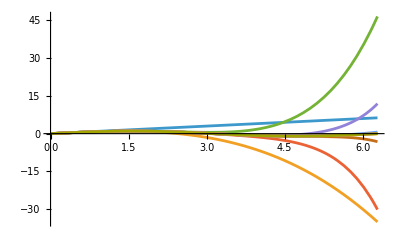

```mathematica
Plot[ funzioni, {x,0,2 Pi}, PlotRange->All]
```

```mathematica
??Plot
```

```mathematica
??Gamma
```

```mathematica
Normal[ Series[ Gamma[x], {x,0,2}]]
```

-EulerGamma+1/x+1/12 (6 EulerGamma^2+π^2) x+1/6 x^2 (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])

```mathematica
Plot3D[ {Re[Gamma[x+I y]], Im[Gamma[x+I y]]}, {x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[th] Cos[phi],Sin[th] Sin[phi],Cos[th]},{th,0,Pi},{phi,0,2 Pi}]
```

-Graphics3D-

```mathematica
comm[m1_,m2_] := m1.m2-m2.m1
```

```mathematica
s[1]={{0,1},{1,0}};
s[2]={{0,-I},{I,0}};
s[3] = {{1,0},{0,-1}};
```

```mathematica
checkpauli = Table[  comm[s[i],s[j]]===2 I Sum[  Signature[{i,j,k}] s[k],{k,1,3}   ]    ,{i,1,3},{j,1,3}]
```

{{True,True,True},{True,True,True},{True,True,True}}

```mathematica
??Plus
```

```mathematica
lista+3
```

{3+a,3+b,3+c}

```mathematica
ggg[b,a]
```

ggg[a,b]

```mathematica
SetAttributes[ggg,Orderless]
```

```mathematica
ggg[b,a]
```

ggg[a,b]

```mathematica
x=3
```

3

```mathematica
f[x_]=a x^2+b
```

9 a+b

```mathematica
g[x_] := a x^2+b
```

```mathematica
f[y]
```

9 a+b

```mathematica
g[y]
```

b+a y^2

```mathematica
MatchQ[ x^2, _^_]
```

False

```mathematica
Clear[x]
```

```mathematica
prova = a x^3 + b x^2 + c x + d
```

d+c x+b x^2+a x^3

```mathematica
prova /. {_^_ -> pippo}
```

d+a pippo+b pippo+c x

```mathematica
prova /. {_^_. -> pippo}
```

pippo

```mathematica
FullForm[x^2]
```

Power[x,2]

```mathematica
FullForm[x]
```

x

```mathematica
prova /. {x^_. -> pippo}
```

d+a pippo+b pippo+c pippo

```mathematica
prova /. {x_^y_ -> g[x,y]}
```

d+c x+b g[x,2]+a g[x,3]

```mathematica
(*  riordino di operatori di creazione e distruzione

    a adagger a  
deve diventare
    adagger a a + a


*)
```

```mathematica
h[x___,a,adagger,y___] := h[x,adagger,a,y] + h[x,y]
```

```mathematica
h[a,a,adagger]
```

2 h[a]+h[adagger,a,a]

```mathematica
Expand[ (a+b)(c+d)]
```

a c+b c+a d+b d

```mathematica
Simplify[ %60]
```

{{True,False,False},{False,True,False},{False,False,True}}

```mathematica
?? Simplify
```

```mathematica
Coefficient[ prova, x, 3]
```

a

```mathematica
prova2 = prova /. x->(1+y)
```

d+c (1+y)+b (1+y)^2+a (1+y)^3

```mathematica
Collect[ prova2, y]
```

a+b+c+d+(3 a+2 b+c) y+(3 a+b) y^2+a y^3

```mathematica
Integrate[ prova, y ]
```

d y+c x y+b x^2 y+a x^3 y

```mathematica
Map[ hh, lista ]
```

{hh[a],hh[b],hh[c]}

```mathematica
(*    integrale di un polinomio   *)

myInt[ expr_, var_] := Module[ {temp},

temp = Expand[expr];
Which[
Head[temp]===Plus,
risultato = Map[ intmonomio[ #, var]&, temp],
True,
risultato = intmonomio[temp, var]
];

risultato
];
```

```mathematica
intmonomio[expr_,var_] := Module[{temp},

If[ MatchQ[expr, p_. var^n_.],
prefattore = expr /. p_. var^n_. -> p;
esponente = expr /. p_. var^n_. -> n;
];

Which[
MatchQ[expr, p_. var^n_.] && FreeQ[ prefattore, var] && FreeQ[ esponente, var] && esponente =!=-1,
risultato = prefattore 1/(esponente+1) var^(esponente+1),

MatchQ[expr, p_. var^n_.] && FreeQ[ prefattore, var] && FreeQ[ esponente, var] && esponente ===-1,
risultato = prefattore Log[var],

FreeQ[ expr, var],
risultato = expr var,

True,
risultato = integra[ expr, var]
];

risultato
];
```

```mathematica
myInt[prova, x]
```

d x+(c x^2)/2+(b x^3)/3+(a x^4)/4

```mathematica
myInt[a/x, x]
```

a Log[x]

```mathematica
myInt[a/x^2, x]
```

-a/x